Scalar ω.b2 = {0.0841357,0.365838,0.871112,1.59427,2.52138,3.64539}

✅  Scalar sector stable

Vector ω.b2 = {0.0338674,0.249249,0.728602,1.47833,2.47211,3.68084}

Tensor ω.b2 = {0.103436,0.442516,1.0349,1.84117,2.78415,3.84736}

✅  Vector sector stable

✅  Tensor sector stable

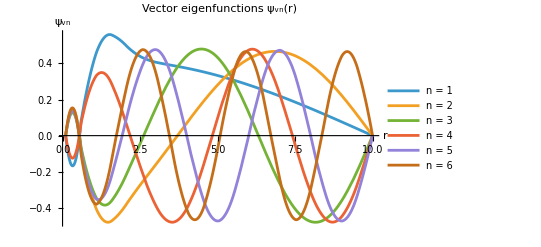

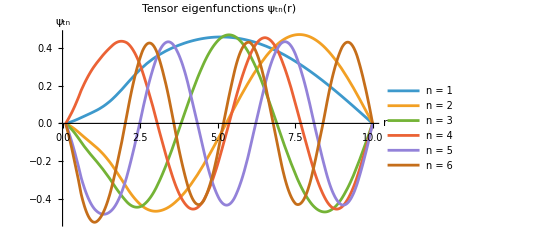

```mathematica
(***********************************************************)(*NEW BLOCK–paste below your scalar-matrix section*)(***********************************************************)(*----------2. Scalar sector via NDEigensystem----------*)rmin=0.1;rmax=10;
nModes=6;

potentialS[r_]:=Φ[r];

Ls=-D[ψs[r],{r,2}]+potentialS[r] ψs[r];
bcS=DirichletCondition[ψs[r]==0,r==rmin||r==rmax];

{valsS,funsS}=NDEigensystem[{Ls,bcS},ψs,{r,rmin,rmax},nModes];

Print["\nScalar ω.b2 = ",valsS//N];
If[AllTrue[valsS,#>0&],Print["✅  Scalar sector stable"],Print["❌  Scalar instability"]];

(*----------3. Vector/Tensor sectors------------------*)
(*Numeric first& second derivatives of Φ*)
dΦ=Function[{x},Evaluate[D[Φ[r],r]/. r->x]];
d2Φ=Function[{x},Evaluate[D[Φ[r],{r,2}]/. r->x]];

Vv[r_]:=-d2Φ[r]+dΦ[r]/r;   (*illustrative vector potential*)
Vt[r_]:=d2Φ[r]+dΦ[r]/r;   (*illustrative tensor potential*)

Lv=-D[ψv[r],{r,2}]+Vv[r] ψv[r];
Lt=-D[ψt[r],{r,2}]+Vt[r] ψt[r];

bcV=DirichletCondition[ψv[r]==0,r==rmin||r==rmax];
bcT=DirichletCondition[ψt[r]==0,r==rmin||r==rmax];

{valsV,funsV}=NDEigensystem[{Lv,bcV},ψv,{r,rmin,rmax},nModes];
{valsT,funsT}=NDEigensystem[{Lt,bcT},ψt,{r,rmin,rmax},nModes];

Print["\nVector ω.b2 = ",valsV//N];
Print["Tensor ω.b2 = ",valsT//N];

If[AllTrue[valsV,#>0&],Print["✅  Vector sector stable"],Print["❌  Vector instability"]];
If[AllTrue[valsT,#>0&],Print["✅  Tensor sector stable"],Print["❌  Tensor instability"]];

(*----------4. Plots------------------------------------*)
Plot[Evaluate@Table[funsV[[k]][r],{k,nModes}],{r,rmin,rmax},PlotLabel->"Vector eigenfunctions ψᵥₙ(r)",PlotLegends->Table["n = "<>ToString[k],{k,nModes}],AxesLabel->{"r","ψᵥₙ"}]

Plot[Evaluate@Table[funsT[[k]][r],{k,nModes}],{r,rmin,rmax},PlotLabel->"Tensor eigenfunctions ψₜₙ(r)",PlotLegends->Table["n = "<>ToString[k],{k,nModes}],AxesLabel->{"r","ψₜₙ"}]
```